# Chapter 5 - Problem 9

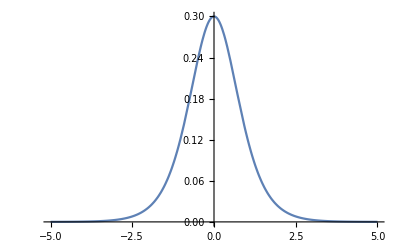

```mathematica
Clear["Global`*"]
(* Constants *)
e = 1.60217 * 10^-19; (* 1 electron volt(ev) = e Joules *)
h = 6.62607004 * 10^-34 ;(* planck's constant *)
m = 9.10938 * 10^-31; (* effective mass of an electron *)
ℏ = h/(2*Pi);
alpha = Sqrt[(2*m*e)/ℏ^2] * 10^-9;
V[x_] = 0.3 * (Sech[x])^2;
Plot[V[x], {x, -5, 5}]
```

```mathematica
di =10/20;
dx = Table[i,{i,-5,5,di}]
```

{-5,-9/2,-4,-7/2,-3,-5/2,-2,-3/2,-1,-1/2,0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5}

```mathematica
vx = V[dx];
k =alpha* Sqrt[en - V [dx]]
```

{5.12316 √(-0.000054475+en),5.12316 √(-0.000148055+en),5.12316 √(-0.000402285+en),5.12316 √(-0.00109227+en),5.12316 √(-0.00295981+en),5.12316 √(-0.00797767+en),5.12316 √(-0.0211952+en),5.12316 √(-0.054212+en),5.12316 √(-0.125992+en),5.12316 √(-0.235934+en),5.12316 √(-0.3+en),5.12316 √(-0.235934+en),5.12316 √(-0.125992+en),5.12316 √(-0.054212+en),5.12316 √(-0.0211952+en),5.12316 √(-0.00797767+en),5.12316 √(-0.00295981+en),5.12316 √(-0.00109227+en),5.12316 √(-0.000402285+en),5.12316 √(-0.000148055+en),5.12316 √(-0.000054475+en)}

```mathematica
PP[kx_,l_] = MatrixExp[-I*kx*l*PauliMatrix[3]];
PI[kL_, kR_] = MatrixExp[1/2*Log[kL/kR] *(PauliMatrix[1] - IdentityMatrix[2])];
```

```mathematica
FullSimplify[PP[kx,l].PI[kL,kR]] // MatrixForm;
```

```mathematica
k[[Length[k]]]
```

5.12316 √(-0.000054475+en)

```mathematica
matelements = Table[PP[k[[index]], di].PI[k[[index]], k[[index+1]]],{index,1,Length[dx]-1}];
```

```mathematica
M = IdentityMatrix[2];
For[index = 1, index <= Length[matelements], index++, M = M.matelements[[index]]]
```

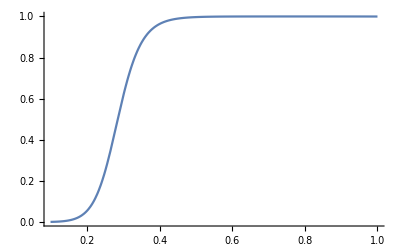

Indeterminate

```mathematica
Plot[Abs[1/M[[1,1]]^2],{en,0.1,1},PlotRange->All]
```